```mathematica
(*          Computer Graphics with Applications of Dr. Makhanov. 
                               Lecture 8  
                       2D Sliders. Interpolation and Flying Objects. (Google's Version)
*)
```

```mathematica
(* To see the entire output, remove occasional suppressing  by ; *)
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,ContourPlot3D, DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,ListLinePlot,ListPointPlot3D,Graphics,Graphics3D}, ImageSize->Medium,AxesLabel->{"x","y","z"}];
```

```mathematica
(* Slider2D controls the position of an object in the (x,y)-plane x=z[[1],y=z[[2]]. Note the Option:  Appearance-> "Labeled" *)
```

```mathematica
R:=1.5
```

```mathematica
xc[t_]:=R Cos[t]
```

```mathematica
yc[t_]:=R Sin[t]
```

```mathematica
Circ[t_,x0_,y0_]:={xc[t],yc[t]}+{x0,y0} (* + x0, y0 ไปเพื่อเปลี่ยนตำแหน่ง (shifting) *)
```

```mathematica
PlotC[x0_,y0_]:=ParametricPlot[Circ[t,x0,y0],{t,0,2 Pi}, PlotRange->{{0,10},{0,10}}]
```

```mathematica
{Slider2D[Dynamic[z],{{0,0},{10,10}},ImageSize->Large,Appearance-> "Labeled"],Dynamic[PlotC[z[[1]],z[[2]]]]}
```

{,}

```mathematica
Options[Slider2D];
```

```mathematica
(* Design a 3D control of a sphere using Slider2D and the Vertical Slider for the z coordinate *)
```

```mathematica
RS10=3;
```

```mathematica
Sphere10[p_]:=Graphics3D[{Purple,Opacity[0.5],Sphere[p,RS10]},Axes->True,PlotRange->-10]
```

```mathematica
S2={Slider2D[Dynamic[xy2],{{-10,-10},{10,10}}, Background->White,ImageSize->Large],Dynamic[xy2]};
```

```mathematica
SV2={VerticalSlider[Dynamic[z2],{-10,10},Background->LightBlue],Dynamic[z2]};
```

```mathematica
SphereControl={Dynamic[Sphere10[{xy2[[1]],xy2[[2]],z2}]],S2,SV2}
```

{,{,},{,}}

```mathematica
(* Interpolation *)
```

```mathematica
(* "Off[]" switches off warning messages from InterpolatingFunction *)
```

```mathematica
Off[InterpolatingFunction::dmval]
```

```mathematica
(* Consider when the list defines the y-values, whereas the x values are integers 1,2,... *)
```

```mathematica
data1:={1,2,5,7,8,-5,6,-3}
```

```mathematica
(* Plot the points *)
```

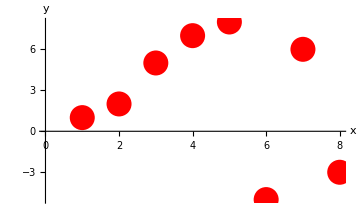

```mathematica
plot1points=ListPlot[data1,PlotStyle->{PointSize[0.05],Red}]
```

```mathematica
(* f15 interpolating functions*)
```

```mathematica
f1=Interpolation[data1,Method->"Spline"];
```

```mathematica
(* Check *)
```

```mathematica
Table[f1[i],{i,Length[data1]}]
```

{1.,2.,5.,7.,8.,-5.,6.,-3.}

```mathematica
(* Plot *)
```

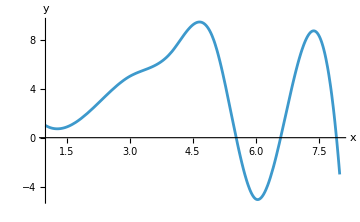

```mathematica
plotf1=Plot[f1[x],{x,1,Length[data1]}]
```

```mathematica
(* Superimpose *)
```

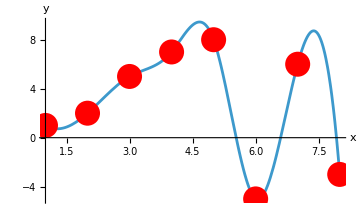

```mathematica
Show[plotf1,plot1points]
```

```mathematica
(* Interpolate an (x,y) data: (x1,y1),(x2,y2),(x3,y3)..... *)
```

```mathematica
data2={{1,1},{2,3},{-1,-3},{7,0},{4,-4}} ;
```

```mathematica
Dimensions[data2]
```

{5,2}

```mathematica
L2=Dimensions[data2][[1]]
```

5

```mathematica
f2=Interpolation[data2,Method->"Spline"];
```

```mathematica
(* Check  *)
```

```mathematica
Table[f2[data2[[i]][[1]]],{i,L2}]
```

{1.,3.,-3.,0.,-4.}

```mathematica
(* Compare *)
```

```mathematica
Transpose[data2][[2]]
```

{1,3,-3,0,-4}

```mathematica
minx=Min[Transpose[data2][[1]]]
```

-1

```mathematica
maxx=Max[Transpose[data2][[1]]]
```

7

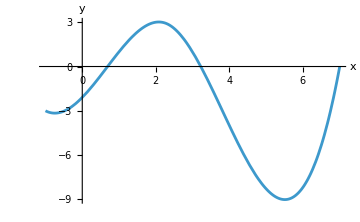

```mathematica
plot2=Plot[f2[x],{x,minx,maxx}]
```

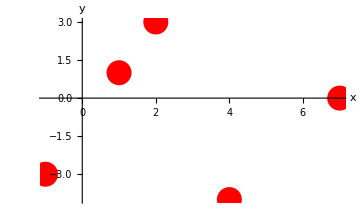

```mathematica
plot2points=ListPlot[data2,PlotStyle->{PointSize[0.05],Red}]
```

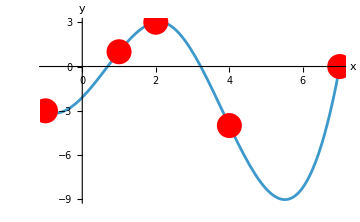

```mathematica
Show[plot2,plot2points]
```

```mathematica
(* Interpolation of the space curves. The 3D spline through the points {{-4,2,4},{4,5,-1},{2,5,0},{1,1,3},{2,-6,-6},{4,4,4}} is defined by data4 *)
```

```mathematica
data4:={{-4,2,4},{4,5,-1},{2,5,0},{1,1,3},{2,-6,-6},{4,4,4}}
```

```mathematica
MatrixForm[data4]
```

(-4 | 2 | 4
4 | 5 | -1
2 | 5 | 0
1 | 1 | 3
2 | -6 | -6
4 | 4 | 4)

```mathematica
x4=Transpose[data4][[1]]
```

{-4,4,2,1,2,4}

```mathematica
y4=Transpose[data4][[2]]
```

{2,5,5,1,-6,4}

```mathematica
z4=Transpose[data4][[3]]
```

{4,-1,0,3,-6,4}

```mathematica
MatrixForm[data4]
```

(-4 | 2 | 4
4 | 5 | -1
2 | 5 | 0
1 | 1 | 3
2 | -6 | -6
4 | 4 | 4)

```mathematica
sx4=Interpolation[x4,Method->"Spline"];
```

```mathematica
sy4=Interpolation[y4,Method->"Spline"];
```

```mathematica
sz4=Interpolation[z4,Method->"Spline"];
```

```mathematica
(* 3D parametric function *)
```

```mathematica
s4[t_]:={sx4[t],sy4[t],sz4[t]}
```

```mathematica
L4=Length[x4];
```

```mathematica
plot4=ParametricPlot3D[s4[t],{t,1,L4},PlotStyle->{Red, Thickness[0.02]},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
plot4points=ListPointPlot3D[data4,PlotStyle->{PointSize[0.07],Blue},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
Show[{plot4,plot4points}]
```

-Graphics3D-

```mathematica
(* 2D trajectory design. Let us spline-interpolate the following data to design a trajectory of the object   *)
```

```mathematica
dataTr = {{1.996668332936563,10.806046117362794},{7.788366846173011,-8.322936730942848},{15.666538192549668,-19.799849932008907},{19.9914720608301,-13.072872417272238},{11.96944288207913,15.673243709264525},{-8.85040886589705,19.20340573300732},{-19.649052252486648,15.078045086866092},{2.330984097009873,-2.9100006761722708}}
```

{{1.99667,10.806},{7.78837,-8.32294},{15.6665,-19.7998},{19.9915,-13.0729},{11.9694,15.6732},{-8.85041,19.2034},{-19.6491,15.078},{2.33098,-2.91}}

```mathematica
MatrixForm[dataTr]
```

(1.99667 | 10.806
7.78837 | -8.32294
15.6665 | -19.7998
19.9915 | -13.0729
11.9694 | 15.6732
-8.85041 | 19.2034
-19.6491 | 15.078
2.33098 | -2.91)

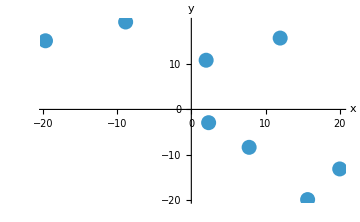

```mathematica
plot1Tr = ListPlot[dataTr, PlotStyle -> PointSize[0.03]]
```

```mathematica
(* Extract x and y and interpolate *)
```

```mathematica
xTr=Transpose[dataTr][[1]]
```

{1.99667,7.78837,15.6665,19.9915,11.9694,-8.85041,-19.6491,2.33098}

```mathematica
yTr=Transpose[dataTr][[2]]
```

{10.806,-8.32294,-19.7998,-13.0729,15.6732,19.2034,15.078,-2.91}

```mathematica
fxTr=Interpolation[xTr,Method->"Spline"];
```

```mathematica
fyTr=Interpolation[yTr,Method->"Spline"];
```

```mathematica
(* parametric function *)
```

```mathematica
fTr[t_]:={fxTr[t],fyTr[t]}  ;
```

```mathematica
MatrixForm[dataTr]
```

(1.99667 | 10.806
7.78837 | -8.32294
15.6665 | -19.7998
19.9915 | -13.0729
11.9694 | 15.6732
-8.85041 | 19.2034
-19.6491 | 15.078
2.33098 | -2.91)

```mathematica
(* Let us plot the trajectory fsp1[t] *)
```

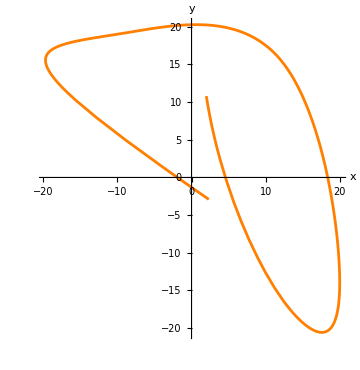

```mathematica
plot2Tr=ParametricPlot[fTr[t],{t,1,Length[xTr]},PlotStyle->Orange]
```

```mathematica
(* Denote the plot of the trajectory and the data by Show1 *)
```

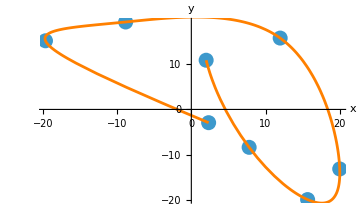

```mathematica
Show1=Show[plot1Tr,plot2Tr]
```

```mathematica
(* Now we move an object along fsp1[t] the same way we moved along the parametric curve designed by a formula  *)
```

```mathematica
(* Objects: Circle, Polygon, RegularPolygon.  We show the trajectory and the interpolating points on the animation plot *)
```

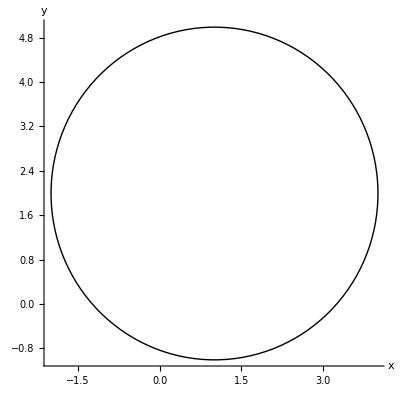

```mathematica
O1=Graphics[Circle[{1,2},3], Axes->True,ImageSize->Tiny]
```

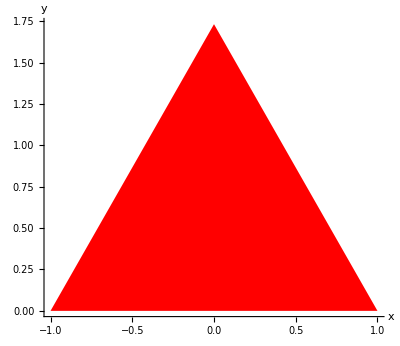

```mathematica
O2=Graphics[{Red,Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]}, Axes->True,ImageSize->Tiny]
```

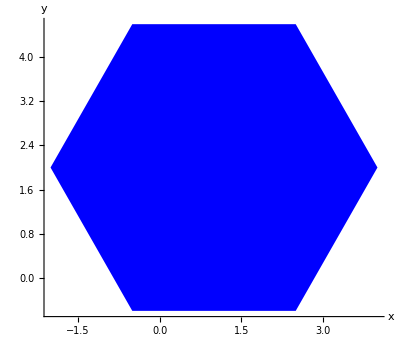

```mathematica
O3=Graphics[{Blue,RegularPolygon[{1,2},3,6]}, Axes->True,ImageSize->Tiny]
```

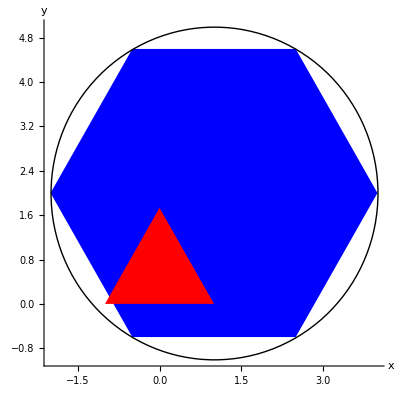

```mathematica
Show[O3,O2,O1]
```

```mathematica
(* Circle with the radius 3.5 at the point fsp1[s]. Understand the difference between 
position control of the primitive Circle and parametric circle (equations)  *)
```

```mathematica
Rs1:=3.5
```

```mathematica
PositionCircle[s_]:=Circle[fTr[s],Rs1]
```

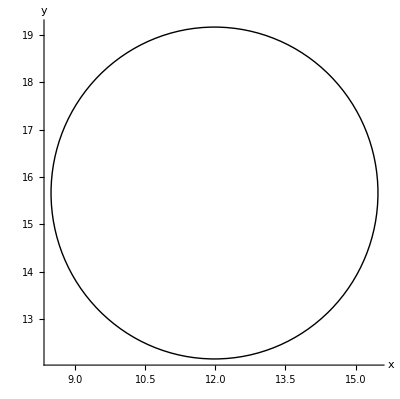

```mathematica
Graphics[PositionCircle[5],Axes->True,ImageSize->Tiny]
```

```mathematica
(* Circle at the point fsp1[s] *)
```

```mathematica
PlotCircle[s_]:=Graphics[PositionCircle[s],PlotRange->{{-20,20},{-20,20}},Axes->True,AspectRatio->1]
```

```mathematica
(* Plot circle at point fsp1[s]. Plot the trajectory and the datapoints *)
```

```mathematica
PlotCircleTrajectory[s_]:=Show[{PlotCircle[s],Show1}]
```

```mathematica
(* Animate *)
```

```mathematica
Manipulate[PlotCircleTrajectory[s],{s,1,Length[xTr],0.01}]
```

```mathematica
(* Pentagon  Primitive RegularPolygon- Memorize!  *)
```

```mathematica
PositionPentagon[s_]:=RegularPolygon[fTr[s],6,5]
```

```mathematica
PlotPentagon[s_]:=Graphics[{Red,PositionPentagon[s]}, Axes->True]
```

```mathematica
PlotPentagonTrajectory[s_]:=Show[{PlotPentagon[s],Show1},PlotRange->25]
```

```mathematica
(* Check. Change to a triangle in class *)
```

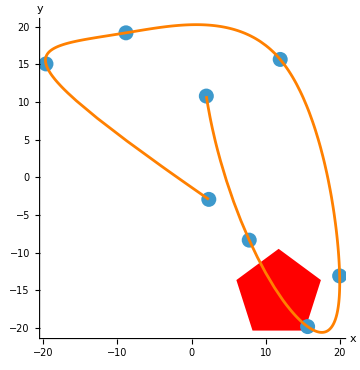

```mathematica
PlotPentagonTrajectory[2.5]
```

```mathematica
Manipulate[PlotPentagonTrajectory[s],{s,1,Length[xTr]}]
```

```mathematica
(* Snoopy: the 2D object is ALSO defined by the datapoints *)
```

```mathematica
datao1:={{1,6},{-4,6},{-8,4},{-10,4},{-8,2},{-10,1},{-11,-2},{-10,-2},{-11,-4},{-7,-2},{-5,0},{-3,4},{-3,0},{-4,-2},{-5,-6},{-4,-8},{-5,-9},{-6,-9},{-7,-8},{-8,-8},{-9,-9},{-5,-13},{-3,-13},{-2,-12},{-2,-11},{-3,-10},{-4,-10},{-3,-9},{-2,-9},{-1,-10},{2,-10},{2,-11},{1,-12},{1,-13},{5,-13},{8,-12},{8,-10},{7,-9},{6,-9},{5,-10},{4,-10},{4,-9},{5,-7},{7,-4},{7,-3},{6,0},{5,2},{1,6},{2,7},{4,6},{5,6},{8,7},{4,10},{8,7},{9,8},{10,10},{9,12},{8,13},{6,13},{4,12},{2,12},{0,10},{2,12},{2,13},{1,15},{0,16},{-2,17},{-4,17},{-6,16},{-7,15},{-8,13},{-8,11},{-7,9},{-6,8},{-4,7},{-1,7},{-1,10},{0,11},{0,12},{1,13},{2,13}}
```

```mathematica
Dimensions[datao1]
```

{81,2}

```mathematica
(* The object is obtained using the same interpolation routines *)
```

```mathematica
xo1=Transpose[datao1][[1]]
```

{1,-4,-8,-10,-8,-10,-11,-10,-11,-7,-5,-3,-3,-4,-5,-4,-5,-6,-7,-8,-9,-5,-3,-2,-2,-3,-4,-3,-2,-1,2,2,1,1,5,8,8,7,6,5,4,4,5,7,7,6,5,1,2,4,5,8,4,8,9,10,9,8,6,4,2,0,2,2,1,0,-2,-4,-6,-7,-8,-8,-7,-6,-4,-1,-1,0,0,1,2}

```mathematica
yo1=Transpose[datao1][[2]]
```

{6,6,4,4,2,1,-2,-2,-4,-2,0,4,0,-2,-6,-8,-9,-9,-8,-8,-9,-13,-13,-12,-11,-10,-10,-9,-9,-10,-10,-11,-12,-13,-13,-12,-10,-9,-9,-10,-10,-9,-7,-4,-3,0,2,6,7,6,6,7,10,7,8,10,12,13,13,12,12,10,12,13,15,16,17,17,16,15,13,11,9,8,7,7,10,11,12,13,13}

```mathematica
fxo1:=Interpolation[xo1,Method->"Spline"]
```

```mathematica
fyo1:=Interpolation[yo1,Method->"Spline"]
```

```mathematica
(* parametric function.*)
```

```mathematica
fspo1[t_]:={fxo1[t],fyo1[t]}
```

```mathematica
(* Snoopy(body) object1 *)
```

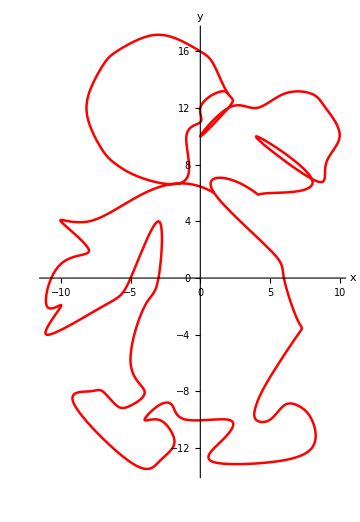

```mathematica
ploto1=ParametricPlot[fspo1[t],{t,1,Length[xo1]},PlotStyle->{Red,Thickness[0.005]}]
```

```mathematica
(* Object2 (ear) *)
```

```mathematica
datao2={{-3,14},{-2,13},{-1,11},{-3,10},{-4,10},{-5,11},{-5,13},{-4,14},{-3,14}}
```

{{-3,14},{-2,13},{-1,11},{-3,10},{-4,10},{-5,11},{-5,13},{-4,14},{-3,14}}

```mathematica
Dimensions[datao2]
```

{9,2}

```mathematica
(* Interpolation of the object 2  *)
```

```mathematica
xo2=Transpose[datao2][[1]];
```

```mathematica
yo2=Transpose[datao2][[2]];
```

```mathematica
fxo2=Interpolation[xo2,Method->"Spline"];
```

```mathematica
fyo2=Interpolation[yo2,Method->"Spline"];
```

```mathematica
fspo2[t_]:={fxo2[t],fyo2[t]}
```

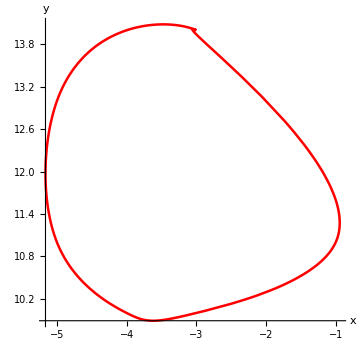

```mathematica
ploto2=ParametricPlot[fspo2[t],{t,1,Length[xo2]},PlotStyle->{Red,Thickness[0.005]}]
```

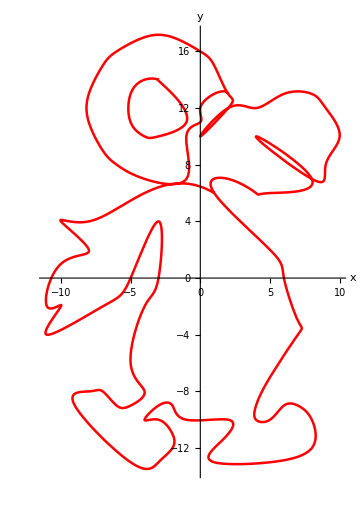

```mathematica
snoopy=Show[ploto1,ploto2]
```

```mathematica
(* Check  *)
```

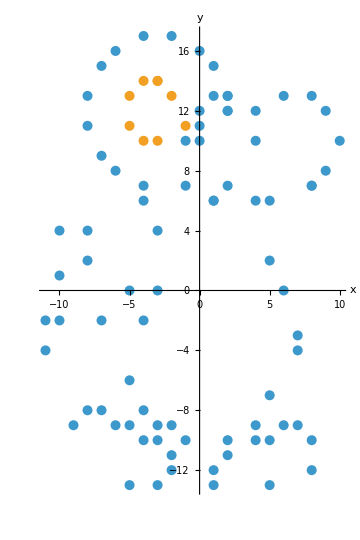

```mathematica
plotdo1=ListPlot[{datao1,datao2},PlotStyle->{PointSize[0.02]},AspectRatio->30/20]
```

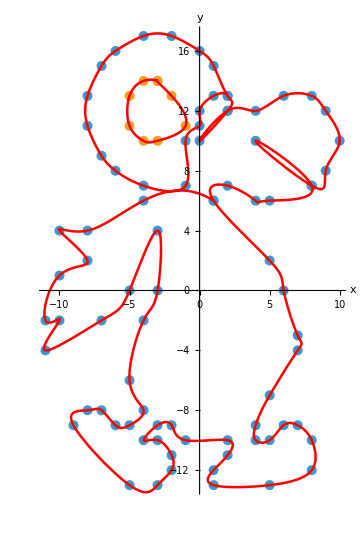

```mathematica
Show[plotdo1,snoopy]
```

```mathematica
(* Let us animate O1 along Snoopy (fspo1[t]). Write a code to move 2 objects fspo1[t] and fspo2[t] along Snoopy by yourself   *)
```

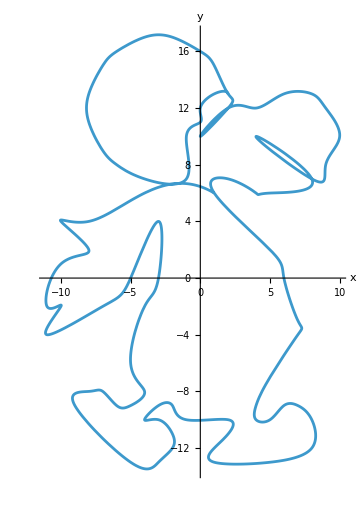

```mathematica
ParametricPlot[fspo1[s],{s,1,Length[xo1]}]
```

```mathematica
ObjectPosition1[s_,t_]:=fspo1[t]+fTr[s]
```

```mathematica
(* Plot the object *)
```

```mathematica
Object1[s_]:=ParametricPlot[ObjectPosition1[s,t],{t,1,Length[xo1]},PlotStyle->{Red,Thickness[0.002]}]
```

```mathematica
(* Now  we plot the trajectory, the data and the object *)
```

```mathematica
ShowO1[s_]:=Show[{Show1,Object1[s]}, PlotRange->30,AspectRatio->1]
```

```mathematica
(* Check. Fix the PlotRange and the AspectRatio *)
```

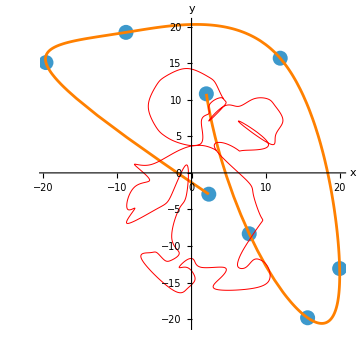

```mathematica
ShowO1[8]
```

```mathematica
(* Animation *)
```

```mathematica
Manipulate[ShowO1[s],{s,1,Length[xTr]}]
```

```mathematica
(* If time allows: A shape given by the primitive or by the formula along a 3D trajectory  *)
```

```mathematica
(* Recall the 3D example based on data 4 *)
```

```mathematica
data4:={{-4,2,4},{4,5,-1},{2,5,0},{1,1,3},{2,-6,-6},{4,4,4}}
```

```mathematica
MatrixForm[data4]
```

(-4 | 2 | 4
4 | 5 | -1
2 | 5 | 0
1 | 1 | 3
2 | -6 | -6
4 | 4 | 4)

```mathematica
x4=Transpose[data4][[1]]
```

{-4,4,2,1,2,4}

```mathematica
y4=Transpose[data4][[2]]
```

{2,5,5,1,-6,4}

```mathematica
z4=Transpose[data4][[3]]
```

{4,-1,0,3,-6,4}

```mathematica
MatrixForm[data4]
```

(-4 | 2 | 4
4 | 5 | -1
2 | 5 | 0
1 | 1 | 3
2 | -6 | -6
4 | 4 | 4)

```mathematica
sx4=Interpolation[x4,Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
sy4=Interpolation[y4,Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
sz4=Interpolation[z4,Method->"Spline"]
```

InterpolatingFunction[…]

```mathematica
(* 3D parametric function *)
```

```mathematica
s4[t_]={sx4[t],sy4[t],sz4[t]} (* immediate evaluation *)
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
L4=Length[x4];
```

```mathematica
plot4=ParametricPlot3D[s4[t],{t,1,L4},PlotStyle->{Red, Thickness[0.02]}]
```

-Graphics3D-

```mathematica
plot4points=ListPointPlot3D[data4,PlotStyle->{PointSize[0.07],Blue}]
```

-Graphics3D-

```mathematica
Show[{plot4,plot4points}]
```

-Graphics3D-

```mathematica
(* Octahedron is a polyhedron with eight flat faces. The Octahedron is one of the five famous Platonic Solids *)
```

```mathematica
(* The Platonic solids are prominent in the philosophy of Plato. Plato introduced them around 360 B.C. (2400 years ago!!!). 
He associated each of the five classical  elements: earth,air,water, fire and aether (the mystical fifth element) 
 corresponding to a certain shape as follows 
 *)
```

```mathematica
(*-Graphics- *)
```

```mathematica
(* -Graphics-*)
```

```mathematica
(* There is a Wolfram function for each of the Platonic solids  *)
```

```mathematica
{Fire=Graphics3D[{Red,Tetrahedron[]}],Graphics3D[{Yellow,Octahedron[]}],Earth=Graphics3D[{Green,Icosahedron[]}], Water=Graphics3D[{Blue,Icosahedron[]}],Aether=Graphics3D[{Brown,Dodecahedron[]}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
MoveOctahedron[P_]:=Graphics3D[{Yellow,Opacity[0.8],Octahedron[P,4]}, Axes->True, PlotLabel->"Octahedron"]
```

```mathematica
MoveOAlongs4[t_]:= MoveOctahedron[s4[t]]
```

```mathematica
(* Check  *)
```

```mathematica
MoveOAlongs4[2]
```

-Graphics3D-

```mathematica
ShowAlls4[t_]:=Show[{plot4,MoveOAlongs4[t]},PlotRange->7]
```

```mathematica
(* Check  *)
```

```mathematica
ShowAlls4[1]
```

-Graphics3D-

```mathematica
ShowAlls4Med[t_]:=Show[ShowAlls4[t]]
```

```mathematica
Manipulate[ShowAlls4Med[s],{s,1,L4}]
```